```mathematica
Graph GraphData
```

```mathematica
GraphDisjointUnion GraphUnion GraphIntersection GraphDifference GraphComplement BooleanGraph
```

```mathematica
EdgeAdd EdgeDelete VertexAdd DirectedEdge UndirectedEdge
EdgeList EdgeCount VertexList AdjacencyMatrix IncidenceMatrix
```

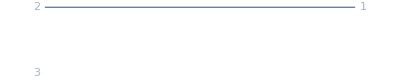

```mathematica
BooleanGraph[And,-Graphics-,-Graphics-,VertexShapeFunction->"Name"]
```

```mathematica
AdjacencyList IncidenceList EdgeRules PlanarFaceList
Rule@@@EdgeList[g] 
AdjacencyMatrix AdjacencyGraph - 矩阵表示和图的创建
IncidenceMatrix KirchhoffMatrix WeightedAdjacencyMatrix
```

AnnotationValue[obj,key]
给出与对象 obj 的 key 关联的注释值
ref/VertexCoordinates

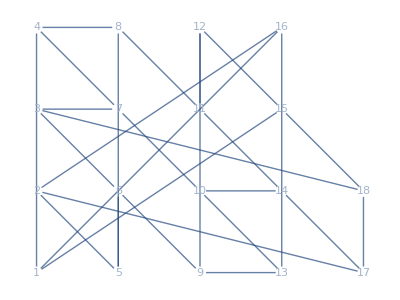

```mathematica
gridLayout[n_]:=Block[{a,b,c},
{a,b,c}={Floor[n^(1/2)],Floor[n/a],Mod[n,a]};
Flatten[Join[Table[{i,j},{i,a},{j,b}],Table[{{a+1,j}},{j,c}]],1]-1
]
GraphPlot[GraphData["PappusGraph"],VertexShapeFunction->"Name",VertexCoordinates->gridLayout[18]]
```

求对两个图进行映射的同构关系：

```mathematica
map=First[Normal[FindGraphIsomorphism[g,h]]]
```

{1→1,2→6,3→4,4→2,5→7,6→5,7→8,8→3}

根据映射关系，对两个图进行突出显示并且添加标签：

```mathematica
a=First/@map;b=Last/@map;
```

```mathematica
highlightGraph[g_,v_]:=HighlightGraph[g,Table[Style[Labeled[v⟦i⟧,v⟦i⟧],ColorData["TemperatureMap"][i/VertexCount[g]]],{i,VertexCount[g]}],VertexSize->Large];
```

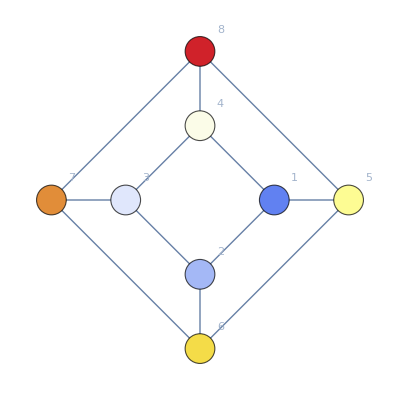
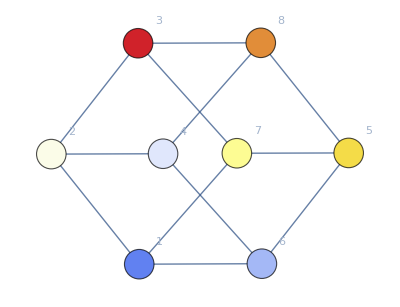

```mathematica
{highlightGraph[g,a],highlightGraph[h,b]}
```

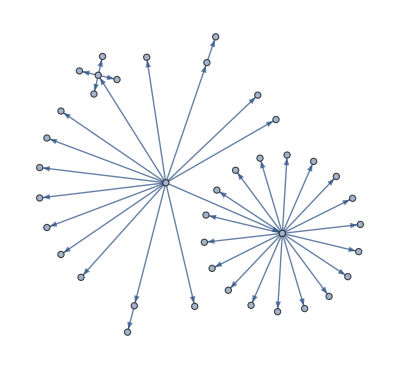

```mathematica
(*文件夹目录的布局 $InstallationDirectory*)
files=Flatten[Rest[NestList[Union[Flatten[Thread[#->FileNames["*",#]]&/@Last/@#]]&,{""->$InstallationDirectory},2]]];
Graph[files, GraphLayout->"BalloonEmbedding"]
```

Johnson Skeleton Graph. Ramsey framework graph

Import, Export — 导入和导出图
“GraphML” ▪  “GXL” ▪  “Graphlet” ▪  “Pajek” ▪  “TGF” ▪  “DOT” ▪  “DIMACS” ▪  “Graph6” ▪  “Sparse6” ▪  “LEDA”

```mathematica
参数式图
CompleteGraph—生成一个完全图或者完全 k 部图
BuckyballGraph ButterflyGraph CirculantGraph CompleteKaryTree CycleGraph DeBruijnGraph GridGraph HararyGraph HararyGraph[k,n]
HypercubeGraph KaryTree KnightTourGraph PetersenGraph StarGraph TorusGraph TuranGraph WheelGraph
```

```mathematica
结构化的图
PathGraph—一般有向或无向路径
TreeGraph—一般有向或无向树
PlanarGraph—一般有向或无向平面图
来自数据的图
RelationGraph—产生基于数据和二进制关系的图
NearestNeighborGraph—为普通元素产生 k 最近邻图
NestGraph—产生嵌套函数图
ExpressionGraph—产生表达式树结构的图
ClusteringTree—根据元素的分层聚类产生树
CayleyGraph  MoleculeGraph  MeshConnectivityGraph MorphologicalGraph
```

```mathematica
RandomGraph[{n,m}]
```

```mathematica
Subgraph NeighborhoodGraph[g,v]
```

```mathematica
ReverseGraph SimpleGraph IndexGraph
VertexReplace—使用规则替换顶点
VertexAdd VertexDelete VertexContract EdgeAdd EdgeDelete EdgeContract
```

```mathematica
BooleanGraph—图的布尔组合
LineGraph—给出线图，其中边变成点，反之亦然
GraphPower—至多 n 步所有顶点相邻接的图
DualPlanarGraph—平面图的对偶
GraphIntersection ▪ GraphUnion ▪ GraphDifference ▪ GraphDisjointUnion ▪ GraphComplement ▪ GraphProduct ▪ GraphJoin ▪ GraphSum
```

GraphProduct[g1,g2,”op”] 给出类型为 “op” 的图的积，其中的边 {u1,u2}<->{v1,v2} 受以下条件限制：
“Cartesian”	(u1==v1 ∧ u2<->v2)∨(u2==v2∧u1<->v1)
“Conormal”	(u1<->v1)∨(u2<->v2)
“Lexicographical”	(u1<->v1)∨(u1==v1∧u2<->v2)
“Normal”	(u1==v1∧u2<->v2)∨(u2==v2∧u1<->v1)∨(u1<->v1∧u2<->v2)
“Rooted”	(u1==v1 ∧ u2<->v2)∨(u1<->v1 ∧ u2==v2==r)
“Tensor”	(u1<->v1)∧(u2<->v2)
顶点 r 为 VertexList[g2] 中的第一个顶点.
GraphProduct[g1,g2] 实际上等价于 GraphProduct[g1,g2,”Cartesian”].
GraphProduct 适用于无向图、有向图、多重图和混合图.